Hadamard Test |

Estimation of the Real Partpaclet:Q3/tutorial/HadamardTest#1760709842 | Estimation of the Imaginary Partpaclet:Q3/tutorial/HadamardTest#1624459610

N.B. This document is still rough. To be elaborated later.

The Hadamard test is a method to estimate the expectation value of a unitary operator.

Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol | The Hadamard gate
ControlledGatepaclet:Q3/ref/ControlledGateQ3 Package Symbol | The controlled-unitary gate
Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol | The measurement on qubits

Quantum circuit elements used in the Hadamard test.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Estimation of the Real Part

To estimate the real part of the expectation value ψUψ, consider a quantum circuit in Figure 1. The probability to get 0 from the measurement is given by

P_0=1/2+1/2 Re[ψUψ]

Therefore, by estimating the probability P_0 through repeated measurements, one can get the estimate of ReψUψ.

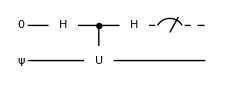

Figure 1. A quantum circuits to estimate ReψUψ.

### Demonstration

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Consider an input state with respect to which we want to get the expectation value of unitary operator U.

```mathematica
in=ProductState[S[2]->c@{0,1},"Label"->Ket@{"ψ"}];
```

Construct the quantum circuit.

```mathematica
qc=QuantumCircuit[
Ket[S@{1}],in,
S[1,6],
ControlledGate[S[1],Rotation[ϕ,S[2,2]],"Label"->"U"],
S[1,6],
Measurement[S[1,3]]
]
```

-Graphics-

Estimation of the Imaginary Part

To estimate the imaginary part of the expectation value ψUψ, we need to slightly modify the quantum circuit in Figure 1 to those in Figure 2. In this case, the probability to get 0 from the measurement is given by

P_0=1/2+1/2 Im[ψUψ] .

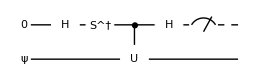
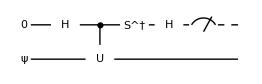

Figure 2. Two equivalent quantum circuits to estimate ImψUψ.

### Demonstration

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Consider an input state with respect to which we want to get the expectation value of unitary operator U.

```mathematica
in=ProductState[S[2]->c@{0,1},"Label"->Ket@{"ψ"}];
```

Construct the quantum circuit.

```mathematica
qc=QuantumCircuit[
Ket[S@{1}],
ProductState[S[2]->c@{0,1},"Label"->Ket@{"ψ"}],
S[1,6],S[1,-7],
ControlledGate[S[1],Rotation[ϕ,S[2,2]],"Label"->"U"],
S[1,6],
Measurement[S[1,3]]
]
```

-Graphics-

Or, equivalently, use the following quantum circuit.

```mathematica
qc=QuantumCircuit[
Ket[S@{1}],
ProductState[S[2]->c@{0,1},"Label"->Ket@{"ψ"}],
S[1,6],
ControlledGate[S[1],Rotation[ϕ,S[2,2]],"Label"->"U"],
S[1,-7],S[1,6],
Measurement[S[1,3]]
]
```

-Graphics-

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Computation: Overview
▪Quantum Algorithms
▪Quantum Information Systems with Q3
▪Demo: Commutation Relations for Qubits

| Related Links
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).